#### Create a big square, divide it by 4 by the centers or each side Throw a virtual dice with 4 values{4 colors, 4 numbers, etc.) Divide again the part that was randomly select Throw the dice again on the remaining parts. If one of the remaining part is selected, divide this part, and forget about the previous one. If the remaining part is not selected at first throw, forget theses cells.

# 尝试1

```mathematica
unit00=Graphics[{Brown,Rectangle[]}];
```

```mathematica
myTable=Table[Graphics[{Brown,Rectangle[]}],{2},{2}];
```

```mathematica
dividedUnit=GraphicsGrid[myTable];
```

```mathematica
graph00=dividedUnit;
```

## Step 1:

```mathematica
valueTable=Table[{a,b},{a,2},{b,2}]
```

{{{1,1},{1,2}},{{2,1},{2,2}}}

```mathematica
randomValue01=Flatten[RandomSample[Flatten[valueTable,1],1]]
```

{1,2}

```mathematica
myTable01=ReplacePart[myTable,randomValue01->dividedUnit];
```

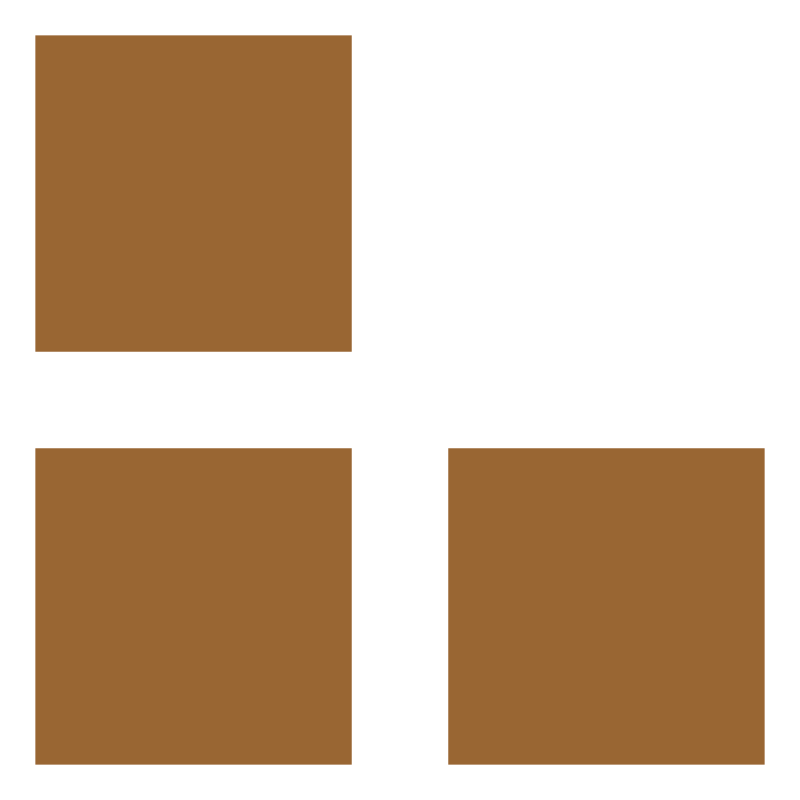

```mathematica
graph01=GraphicsGrid[myTable01]
```

```mathematica
a≠b
```

a≠b

## Step 2

```mathematica
randomValue02=Flatten[RandomSample[Flatten[valueTable,1],1]]
randomValue03=Flatten[RandomSample[Flatten[valueTable,1],1]]
```

{1,1}

{1,2}

## 卡在语法，不知道怎么表示复杂的条件语句

```mathematica
myTable02=ReplacePart[myTable01,{randomValue02/;(randomValue02≠randomValue01)->dividedUnit,randomValue01/;(randomValue02≠randomValue01)->unit00}];
```

```mathematica
myTable02[[randomValue02]];
```

```mathematica
myTable02=ReplacePart[myTable02,{{{2,1},{1,2}}->dividedUnit}];
```

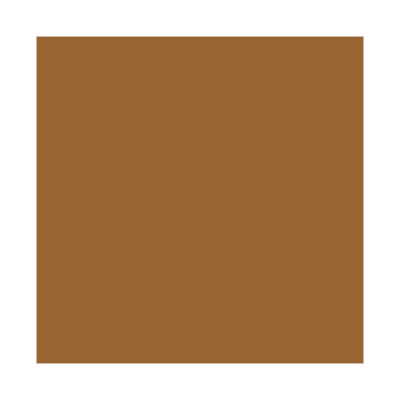

```mathematica
graph02=GraphicsGrid[myTable02]
```

## 尝试2

```mathematica
RandomChoice[{a,b,c,d}]
```

d

```mathematica
Counts[Table[RandomChoice[{a,b,c,d}],10000]]
```

<|b→2442,d→2541,a→2570,c→2447|>

```mathematica
myRandomFunction=RandomChoice[{a,b,c,d}]
```

a

```mathematica
Table[RandomChoice[{a,b,c,d}],10]
If[a,Rectangle[{0,0},{0.5,0.5}]]
If[b,Rectangle[{0.5,0},{1,0.5}]]
If[c,Rectangle[{0,0.5},{0.5,1}]]
If[d,Rectangle[{0.5,0.5},{1,1}]]
```

{c,b,a,a,c,c,d,a,b,c}

If[a,Rectangle[{0,0},{0.5,0.5}]]

If[b,Rectangle[{0.5,0},{1,0.5}]]

If[c,Rectangle[{0,0.5},{0.5,1}]]

If[d,Rectangle[{0.5,0.5},{1,1}]]

# 老师思路

## foldlist 适用于两个变量的函数

```mathematica
Table[RandomChoice[{a,b,c,d}],10]
```

{b,a,d,b,b,c,b,c,b,a}

```mathematica
Clear[a,b,c,d,x,f];
FoldList[f,x,{a,b,c,d,e}]
```

{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c],f[f[f[f[x,a],b],c],d],f[f[f[f[f[x,a],b],c],d],e]}

## x是初始值，abcd是shift值,这里可以print[i]来检查i是如何运行的

```mathematica
x={0,0};
c={0,0};
a={0,0.5};
b={0.5,0.5};
d={0.5,0};
```

```mathematica
f[x_,y_]:=x+y;
```

```mathematica
i=0;
FoldList[f[#1,#2/(aa=2^i++); Print[aa]]&,x,Table[RandomChoice[{a,b,c,d}],10]]
```

1

2

4

8

16

32

64

128

256

512

{{0,0},{Null,Null},{2 Null,2 Null},{3 Null,3 Null},{4 Null,4 Null},{5 Null,5 Null},{6 Null,6 Null},{7 Null,7 Null},{8 Null,8 Null},{9 Null,9 Null},{10 Null,10 Null}}

## 然后再删掉print

```mathematica
i=0;
FoldList[f[#1,#2/(aa=2^i++)]&,x,{b,b,b,b,b,b,b,b}]
```

{{0,0},{0.5,0.5},{0.75,0.75},{0.875,0.875},{0.9375,0.9375},{0.96875,0.96875},{0.984375,0.984375},{0.992188,0.992188},{0.996094,0.996094}}

```mathematica
i=0;
centerPoint=FoldList[f[#1,#2/(aa=2^i++)]&,x,Table[RandomChoice[{a,b,c,d}],10]]
```

{{0,0},{0,0.5},{0.25,0.75},{0.375,0.75},{0.375,0.8125},{0.40625,0.84375},{0.421875,0.859375},{0.429688,0.859375},{0.429688,0.863281},{0.431641,0.863281},{0.431641,0.863281}}

```mathematica
{RandomColor[],Rectangle[#]}&/@centerPoint
```

{{RGBColor[0.47084627506547916, 0.6087647938493952, 0.9145649476566771],Rectangle[{0,0}]},{RGBColor[0.3735157512456677, 0.21541000411219757, 0.2879664356831628],Rectangle[{0,0}]},{RGBColor[0.7798685868262913, 0.2647780242270583, 0.74953780011825],Rectangle[{0,0}]},{RGBColor[0.24011356117880345, 0.28206776066359773, 0.5738137379749986],Rectangle[{0.125,0.125}]},{RGBColor[0.7276872857374226, 0.9766697608900714, 0.41252900990592556],Rectangle[{0.125,0.125}]},{RGBColor[0.07125094697367906, 0.4377829004520053, 0.486063924099565],Rectangle[{0.15625,0.125}]},{RGBColor[0.5678358258614045, 0.018495422895698388, 0.6226607145883924],Rectangle[{0.15625,0.140625}]},{RGBColor[0.8342517713505, 0.07269025202220458, 0.10420958202821273],Rectangle[{0.15625,0.140625}]},{RGBColor[0.2707907517102055, 0.017460910613457337, 0.02536740752638944],Rectangle[{0.15625,0.144531}]},{RGBColor[0.7447960706666348, 0.5310675963838407, 0.9628069221795412],Rectangle[{0.158203,0.146484}]},{RGBColor[0.2890562098768368, 0.5957756563882723, 0.3612666313217354],Rectangle[{0.158203,0.147461}]}}

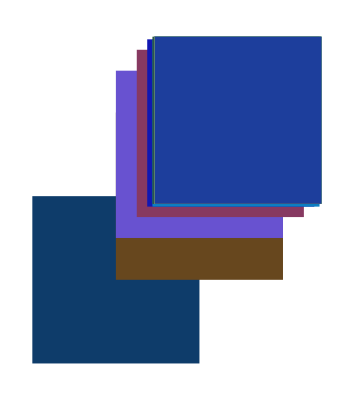

```mathematica
Graphics[%]
```

```mathematica
centerPoint
```

{{0,0},{0,0.5},{0.25,0.75},{0.375,0.75},{0.375,0.8125},{0.40625,0.84375},{0.421875,0.859375},{0.429688,0.859375},{0.429688,0.863281},{0.431641,0.863281},{0.431641,0.863281}}

```mathematica
sideVector={1,1};
k=0;
myArea=centerPoint/.({a_,b_}):>{{a,b},{a,b}+sideVector/(2^(k++))}
```

{{{0,0},{1,1}},{{0,0.5},{1/2,1.}},{{0.25,0.75},{0.5,1.}},{{0.375,0.75},{0.5,0.875}},{{0.375,0.8125},{0.4375,0.875}},{{0.40625,0.84375},{0.4375,0.875}},{{0.421875,0.859375},{0.4375,0.875}},{{0.429688,0.859375},{0.4375,0.867188}},{{0.429688,0.863281},{0.433594,0.867188}},{{0.431641,0.863281},{0.433594,0.865234}},{{0.431641,0.863281},{0.432617,0.864258}}}

## 这里注意数据结构和语法，以下两种都不能搞定，通过第三种方法来取消结构层次

```mathematica
Rectangle/@myArea
```

{Rectangle[{{0,0},{1,1}}],Rectangle[{{0,0.5},{1/2,1.}}],Rectangle[{{0.25,0.75},{0.5,1.}}],Rectangle[{{0.375,0.75},{0.5,0.875}}],Rectangle[{{0.375,0.8125},{0.4375,0.875}}],Rectangle[{{0.40625,0.84375},{0.4375,0.875}}],Rectangle[{{0.421875,0.859375},{0.4375,0.875}}],Rectangle[{{0.429688,0.859375},{0.4375,0.867188}}],Rectangle[{{0.429688,0.863281},{0.433594,0.867188}}],Rectangle[{{0.431641,0.863281},{0.433594,0.865234}}],Rectangle[{{0.431641,0.863281},{0.432617,0.864258}}]}

```mathematica
Rectangle/@Flatten[myArea,1]
```

{Rectangle[{0,0}],Rectangle[{1,1}],Rectangle[{0,0.5}],Rectangle[{1/2,1.}],Rectangle[{0.25,0.75}],Rectangle[{0.5,1.}],Rectangle[{0.375,0.75}],Rectangle[{0.5,0.875}],Rectangle[{0.375,0.8125}],Rectangle[{0.4375,0.875}],Rectangle[{0.40625,0.84375}],Rectangle[{0.4375,0.875}],Rectangle[{0.421875,0.859375}],Rectangle[{0.4375,0.875}],Rectangle[{0.429688,0.859375}],Rectangle[{0.4375,0.867188}],Rectangle[{0.429688,0.863281}],Rectangle[{0.433594,0.867188}],Rectangle[{0.431641,0.863281}],Rectangle[{0.433594,0.865234}],Rectangle[{0.431641,0.863281}],Rectangle[{0.432617,0.864258}]}

```mathematica
{RandomColor[],Opacity[0.5],Rectangle[#[[1]],#[[2]]]}&/@myArea
```

{{RGBColor[0.842097726336285, 0.0949596742341825, 0.7111058860055566],Opacity[0.5],Rectangle[{0,0},{1,1}]},{RGBColor[0.9022376569460049, 0.9347278034403288, 0.48933159339567256],Opacity[0.5],Rectangle[{0,0.5},{1/2,1.}]},{RGBColor[0.5098743088979305, 0.36386061868722575, 0.20105210339169388],Opacity[0.5],Rectangle[{0.25,0.75},{0.5,1.}]},{RGBColor[0.807613151926927, 0.16382810150891713, 0.28200443923623486],Opacity[0.5],Rectangle[{0.375,0.75},{0.5,0.875}]},{RGBColor[0.45937778977748867, 0.7556512776150652, 0.22192012768005753],Opacity[0.5],Rectangle[{0.375,0.8125},{0.4375,0.875}]},{RGBColor[0.7121462711146251, 0.4794751821877181, 0.8985176250199898],Opacity[0.5],Rectangle[{0.40625,0.84375},{0.4375,0.875}]},{RGBColor[0.1436608636094121, 0.8527493818384038, 0.015282452692145121],Opacity[0.5],Rectangle[{0.421875,0.859375},{0.4375,0.875}]},{RGBColor[0.7197337749713455, 0.5337519003012476, 0.16603766018833555],Opacity[0.5],Rectangle[{0.429688,0.859375},{0.4375,0.867188}]},{RGBColor[0.22131680548206845, 0.16622745062476318, 0.8499974396653569],Opacity[0.5],Rectangle[{0.429688,0.863281},{0.433594,0.867188}]},{RGBColor[0.16817411931503656, 0.04947313018971977, 0.6333589414735956],Opacity[0.5],Rectangle[{0.431641,0.863281},{0.433594,0.865234}]},{RGBColor[0.7989096068102712, 0.9996002329686742, 0.5015639244040027],Opacity[0.5],Rectangle[{0.431641,0.863281},{0.432617,0.864258}]}}

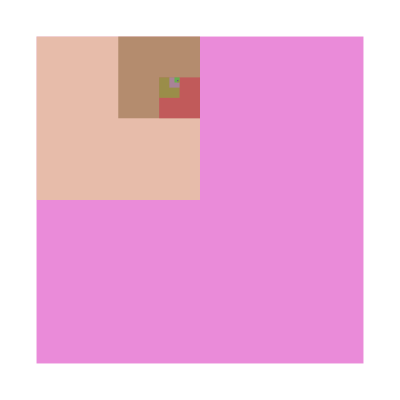

```mathematica
Graphics[%]
```

```mathematica
If[If[
```